Chaotic communication experiment.
In all such chaos computations one should wonder whether the attendant floating-point precision is sufficient. Such is the intrinsic and natural computational demand of chaotic dynamics.

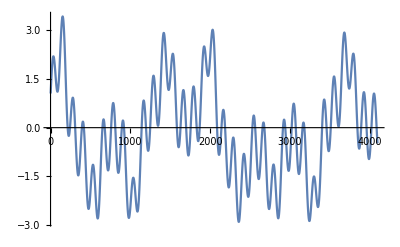

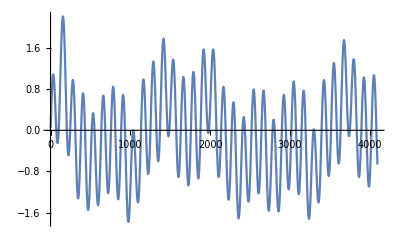

```mathematica
σ = 16; r = 46.5; b = 4;
dt = 0.001;
len = 4096;
(* The signal to be sent *)
x[q_]= N[Sin[q/20]];   
U = V = W = 1.0;
s =Table[0,{len}];
Do[
dU = σ (V-U);
dV  = r U - V - 20 U W;
dW  = 5 U V - b W;
{U,V,W} += {dU,dV,dW} dt;
s[[q]] = x[q] + U,
{q,1,len}];

(* Next, show the transmitted signal. *)
ListPlot[s, Joined->True, Ticks->None]

(* Next, run the receiver using List s as the input *)
u = v = w = 1.0;
r = 30;
X = Table[0, {len}];
Do[
du = σ (v - u);
dv  = r s[[q]] - v - 20 s[[q]] w;
dw  =5 s[[q]] v - b w;
{u,v,w} += {du,dv,dw} dt;
X[[q]]=s[[q]]-u,
{q,1,len}
];
ListPlot[X, Joined->True,Ticks->None]
```